Intro to Quantum Mechanics Homework 2 Question 4: Philip Lucas

Part A normalization constant for the ground state.

Defining the wavefunction from Griffiths “Introduction to Quantum Mechanics Second Edition” Page 46

```mathematica
f[x_]=A*E^(-m*ω (x^2)/(2*ℏ))
```

A ⅇ^(-(m x^2 ω)/(2 ℏ))

Normalizing the wave function requires finding it squared and integrating. That integral must equal one  Then solving for the Cofficient A

```mathematica
Solve[Integrate[f[x]^2,{x,-∞,∞},Assumptions->Re[(m*ω)/ℏ]>0]==1,A]
```

{{A→-((m ω)/ℏ)^(1/4)/π^(1/4)},{A→((m ω)/ℏ)^(1/4)/π^(1/4)}}

We know that we just want the positive value because it should be the absolute value of A squared.

```mathematica
Coefficent = ((m ω)/(π*ℏ))^(1/4)
```

((m ω)/ℏ)^(1/4)/π^(1/4)

This matches the Coefficient found in the Griffiths “Introduction to Quantum Mechanics Second Edition” Textbook pg 46 Eq (2.59) solution.

```mathematica
Φ[x_] = Coefficent*f[x]/A
```

(ⅇ^(-(m x^2 ω)/(2 ℏ)) ((m ω)/ℏ)^(1/4))/π^(1/4)

Checking normalization. Re-integrating the wave function squared should give 1

```mathematica
Integrate[Φ[x]^2,{x,-∞,∞},Assumptions->Re[(m*ω)/ℏ]>0]
```

1

The seems to check out. That is the desired outcome after normalization

Part 2 Solving for the wave function in the n = 2 state

Defining operators and wave functions

```mathematica
Subscript[p, x] := -I*ℏ* D[#, x] &; 
Subscript[a, raising] := (√(1/(2*ℏ*m*ω))) (-I*Subscript[p, x]@# + m*ω*x #) &; 
Subscript[a, lowering]:=(√(1/(2*ℏ*m*ω))) (I*Subscript[p, x]@#+m*ω*x #)&;
Subscript[Φ, 1]=Simplify[C*(1/√(1!))*Subscript[a, raising]@Φ[x]]
```

(√2 C ⅇ^(-(m x^2 ω)/(2 ℏ)) x √(1/(m ω ℏ)) ((m ω)/ℏ)^(5/4) ℏ)/π^(1/4)

```mathematica
Subscript[Φ, 2]=Simplify[C*(1/√(2!))*Subscript[a, raising]@Subscript[a, raising]@Φ[x]]
```

(C ⅇ^(-(m x^2 ω)/(2 ℏ)) (2 m x^2 ω-ℏ) ((m ω)/ℏ)^(1/4))/(√2 π^(1/4) ℏ)

Testing that I can stack operators like I think I can in Mathematica

```mathematica
Subscript[Φ, 2t]=Simplify[C*(1/√(2!))*Subscript[a, raising]@Subscript[Φ, 1]]
```

(C^2 ⅇ^(-(m x^2 ω)/(2 ℏ)) (2 m x^2 ω-ℏ) ((m ω)/ℏ)^(1/4))/(√2 π^(1/4) ℏ)

```mathematica
Solve[Integrate[Subscript[Φ, 2]^2,{x,-∞,∞},Assumptions->Re[(m*ω)/ℏ]>0]==1,C]
```

```mathematica
{{C->-1},{C->1}}
```

```mathematica
Subscript[Φ, n=2]=Simplify[(1/√(2!))*Subscript[a, raising]@Subscript[a, raising]@Φ[x]]
```

(ⅇ^(-(m x^2 ω)/(2 ℏ)) (2 m x^2 ω-ℏ) ((m ω)/ℏ)^(1/4))/(√2 π^(1/4) ℏ)

making a plot just to see the wave shapes and compare to expected. treating all undefined symbols as equalling 1

```mathematica
ff = (E^(-((x^2 )/(2)))/π^(1/4))
Integrate[ff^2,{x,-∞,∞}]
```

(ⅇ^(-x^2/2))/π^(1/4)

1

```mathematica
tt = (E^(-((x^2)/(2))) (2x^2-1)/(Sqrt[2] π^(1/4)))
```

```mathematica
(ⅇ^(-x^2/2) (-1+2 x^2))/(√2 π^(1/4))
```

```mathematica
gg = (Sqrt[2]  E^(-(( x^2 )/(2 ))) x Sqrt[1/1] (1)^(5/4) 1)/π^(1/4)
```

(√2 ⅇ^(-x^2/2) x)/π^(1/4)

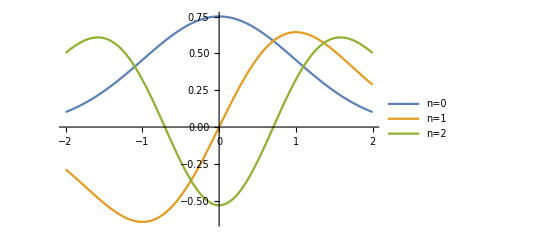

```mathematica
Plot[{ff,gg,tt},{x,-2,2},PlotLegends->{"n=0","n=1","n=2"}]
```

Without plugging in values for  m,ω and,ℏ . I set them all to 1.These are the shapes I’d expect in relation to a quadratic well. The agree with the wave shapes seen on pg 58 figure 2.7(a) of Griffiths “Introduction to Quantum Mechanics 2nd Edition”. As a result I feel pretty confident in my solutions for this problem.